```mathematica
(*Plot the surface*)
ParametricPlot3D[{r Cos[theta],r Sin[theta],r},{r,0,2},{theta,0,2 Pi},PlotRange->All,AxesLabel->{"x","y","z"},MeshFunctions->{#4&,#5&},MeshStyle->{{Thick,Red},{Thick,Blue}}]
```

-Graphics3D-

```mathematica
(*Define the parametric functions*)r[rVal_,thetaVal_]:={rVal Cos[thetaVal],rVal Sin[thetaVal],thetaVal}

(*Compute the partial derivatives with respect to r and theta*)
rr=D[r[rVal,thetaVal],rVal];
rTheta=D[r[rVal,thetaVal],thetaVal];

(*Compute the magnitude of the cross product of rr and rTheta*)
magnitudeCrossProduct=Norm[Cross[rr,rTheta]];

(*Integrate over the region D*)
area=Integrate[magnitudeCrossProduct,{rVal,0,1},{thetaVal,0,2 Pi}];

(*Simplify the expression using the relationship between arsinh and ln*)
simplifiedArea=Simplify[area,Assumptions->x>0];
simplifiedArea
```

π (√2+ArcSinh[1])

π (√2+ArcSinh[1])

π (√2+ArcSinh[1])

ArcSinh[1]

ArcSinh[1]

```mathematica
Clear[rTheta,rTheta,magnitudeCrossProduct,area,r,rdius,rc]
(*Define the parametric functions*)rc[theta_,r_]:={Cos[theta] r,Sin[theta] r,theta}

(*Compute the partial derivatives with respect to theta and phi*)
rTheta=D[rc[theta,r],theta]
rdius=D[rc[theta,r],r]

(*Compute the magnitude of the cross product of rTheta and rPhi*)
magnitudeCrossProduct=Norm[Cross[rTheta,rdius]];

(*Integrate over the region D*)
area=Integrate[magnitudeCrossProduct,{theta,0,3 Pi},{r,0,1}];

area
```

{-r Sin[theta],r Cos[theta],1}

{Cos[theta],Sin[theta],0}

3/2 π (√2+ArcSinh[1])

```mathematica
(*Clear all variables*)ClearAll["Global`*"]

(*Define the parametric functions for the torus*)
r[theta_,phi_,R_]:={(R+Cos[phi]) Cos[theta],(R+Cos[phi]) Sin[theta],Sin[phi]}

(*Compute the partial derivatives with respect to theta and phi*)
rTheta=D[r[theta,phi,R],theta]
rPhi=D[r[theta,phi,R],phi]

(*Compute the magnitude of the cross product of rTheta and rPhi*)
magnitudeCrossProduct=Simplify[Norm[Cross[rTheta,rPhi]],{R>1,Element[R,Reals]}];

(*Integrate over the region D*)
area=Integrate[magnitudeCrossProduct,{theta,0,2 Pi},{phi,0,2 Pi},Assumptions->{R>1,Element[R,Reals]}];

area
```

{-((R+Cos[phi]) Sin[theta]),(R+Cos[phi]) Cos[theta],0}

{-Cos[theta] Sin[phi],-Sin[phi] Sin[theta],Cos[phi]}

4 π^2 R

```mathematica
(*Clear all global variables and definitions*)ClearAll["Global`*"]

(*Define the parametric functions for the torus*)
r[theta_,phi_,R_]:={(R+Cos[phi]) Cos[theta],(R+Cos[phi]) Sin[theta],Sin[phi]}

(*Use Manipulate to create an interactive plot with a slider for R*)
Manipulate[ParametricPlot3D[r[theta,phi,R],{theta,0,2 Pi},{phi,0,2 Pi},PlotRange->{{-R-2,R+2},{-R-2,R+2},{-2,2}},MeshFunctions->{#4&,#5&},MeshStyle->{{Thick,Red},{Thick,Blue}},AxesLabel->{"x","y","z"},Boxed->False],{{R,2,"Radius R"},1.1,5}]
```

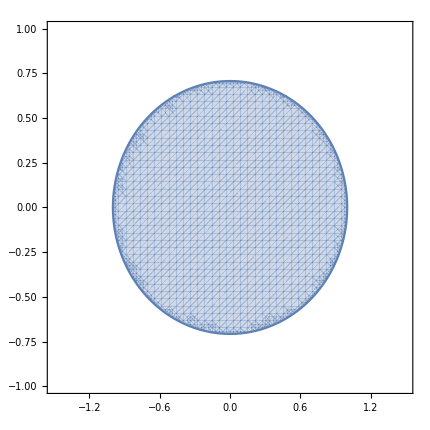

```mathematica
(*Clear all global variables and definitions*)ClearAll["Global`*"]

(*Plot the region using RegionPlot*)
RegionPlot[x^2+2 y^2<=1,{x,-1.5,1.5},{y,-1,1},PlotPoints->50]
```

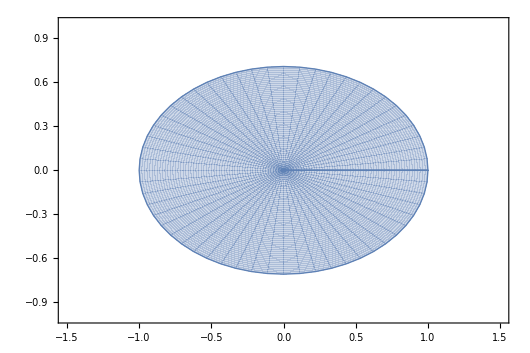

```mathematica
(*Clear all global variables and definitions*)ClearAll["Global`*"]

(*Plot the region using ParametricPlot*)
ParametricPlot[{r Cos[t],r Sin[t]/Sqrt[2]},{t,0,2 Pi},{r,0,1},PlotRange->{{-1.5,1.5},{-1,1}},Mesh->None]
```